# Driven-SQUID Toric Code: Testing What the Certificate Takes on Trust

Mohammad Bahrami • 2026

The preprint arXiv:2611.03329 proposes a method for verifying that a proposed device design reproduces a quantum error-correcting code at low energy, before the device is built; its test case is the toric code. For the toric code, the device Hamiltonian must have four lowest eigenstates, separated from all others by an energy gap, spanning a space close to the code's protected space up to a fixed rotation of each qubit. AI agents search the device parameters and simulate the device, and the Lean proof checker certifies that the difference between the simulated Hamiltonian and the ideal one, plus a declared numerical tolerance, is too small to close the gap. The certificate starts from the Pauli coefficients of the effective Hamiltonian, which come from the simulation: it verifies neither the circuit model behind these coefficients nor whether the tolerance covers the simulation's numerical error, and the authors cover both by human review. This notebook tests that model with exact formulas: the coupler's Josephson cosine is exactly a sum of 16 Pauli products with closed-form coefficients. The formulas reproduce the preprint's simulated four-qubit coupling, and find five things the certificate does not test: through the transmon formulas, the single coupler's parameters break a condition the preprint sets for the eight-qubit array; the main text and the supplement write different Josephson terms, and with the supplement's the four-qubit term linear in the drive vanishes; the drive makes some unwanted transitions resonant at the listed frequencies; a small unwanted term can still split or rotate the protected states; and one excitation in the coupler reverses the sign of the four-qubit term.

## The Question: What Does the Certificate Take on Trust?

The preprint arXiv:2611.03329 [1] proposes a method for verifying that a proposed device design reproduces a quantum error-correcting code at low energy, before the device is built. A quantum error-correcting code stores a few qubits in the joint state of many physical qubits, so that an error on one physical qubit can be detected and undone. The preprint's test case is the toric code on eight qubits, which stores two. The toric code is specified by a Hamiltonian, the target Hamiltonian, a sum of eight four-qubit Pauli products, products of X̂, Ŷ or Ẑ on four qubits. Its four lowest states are separated from all others by an energy gap, and they span the protected space: the space that holds the two stored qubits. The device is driven periodically, so the method describes it by its effective Hamiltonian: the time-independent Hamiltonian that produces the same evolution over one drive period as the device does. The method verifies that the effective Hamiltonian also has four lowest eigenstates, separated from all others by an energy gap, and that they span a space close to the protected space, up to a fixed rotation of each qubit.

The eight qubits sit on the edges of a 2×2 square grid wrapped onto a torus. Four of the terms are stars, X̂ on the four edges that meet at a vertex, and four are plaquettes, Ẑ on the four edges around a face. Draw the grid with TorusGraph, number each edge by its qubit in the preprint's supplementary Table S1, and label each vertex with its star:

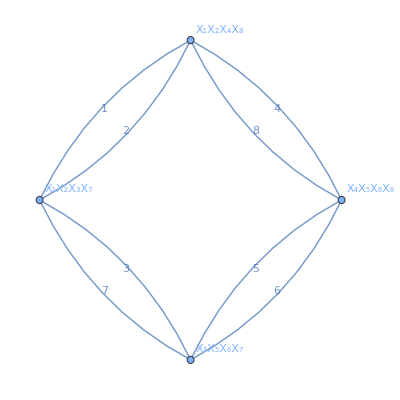

```mathematica
qubitOf[L_][i_] := With[{r = Quotient[Ceiling[i/2] - 1, L], c = Mod[Ceiling[i/2] - 1, L]}, 2 L r + c + 1 + If[OddQ[i], L, 0]];
toricGraph[L_, opts___] := With[{g = TorusGraph[{L, L}]}, EdgeTaggedGraph[VertexList[g], EdgeList[g] -> Array[qubitOf[L], EdgeCount[g]], opts]];
starLabel[g_, v_] := Row[Subscript["X", #] & /@ Sort[Last /@ IncidenceList[g, v]]];
With[{g = toricGraph[2]}, toricGraph[2, EdgeLabels -> "EdgeTag", VertexLabels -> (# -> starLabel[g, #] & /@ VertexList[g])]]
```

The plaquettes are faces, which a graph does not hold. On the torus itself each plaquette is the patch of surface enclosed by its four edges. Draw the grid there, from above and from below, reading each star off the edges that meet at a vertex and each plaquette off the edges around a face:

```mathematica
toricTorus[L_] := With[{a = 1, R = 3, sites = Tuples[Range[0, L - 1], 2], qubits = Range[2 L^2]},
  Block[{edge, mid, star, plaquette, T, patch, product, color},
   edge[q_] := With[{r = Quotient[q - 1, 2 L], d = Quotient[Mod[q - 1, 2 L], L], c = Mod[q - 1, L]}, {{r, c}, {r, c} + If[d == 0, {0, 1}, {1, 0}]}];
   mid[q_] := Mean[edge[q]];
   star[s_] := Select[qubits, MemberQ[Mod[edge[#], L], s] &];
   plaquette[f_] := Select[qubits, MemberQ[Mod[f + {1/2, 1/2} + # , L] & /@ {{1/2, 0}, {-1/2, 0}, {0, 1/2}, {0, -1/2}}, Mod[mid[#], L]] &];
   T[rad_][{r_, c_}] := SurfaceData["Torus", "ParametricEquations"][rad, R] @@ (2 Pi {c, r}/L);
   patch[f_, n_] := With[{p = Table[T[a][f + {s, t}], {s, Subdivide[0, 1, n]}, {t, Subdivide[0, 1, n]}]},
     Polygon[Flatten[Table[{p[[i, j]], p[[i + 1, j]], p[[i + 1, j + 1]], p[[i, j + 1]]}, {i, n}, {j, n}], 1]]];
   product[x_, s_] := Row[Subscript[x, #] & /@ s];
   color[k_] := ColorData[97][k];
   Graphics3D[{
     MapIndexed[{Opacity[0.75], Lighter[color[First[#2]], 0.35], EdgeForm[], patch[#1, 12]} &, sites],
     {GrayLevel[0.3], Tube[T[1.03 a] /@ Subdivide[#1, #2, 24], 0.045] & @@@ (edge /@ qubits)},
     {Black, Text[Style[#, 13, Bold], T[1.3 a][mid[#]]] & /@ qubits},
     {Red, Sphere[T[1.03 a][#], 0.13], Text[Style[product["X", star[#]], 12], T[1.75 a][#]]} & /@ sites,
     MapIndexed[Text[Style[product["Z", plaquette[#1]], 12, Darker[color[First[#2]]]], T[1.75 a][#1 + {1/2, 1/2}]] &, sites]},
    Boxed -> False, Lighting -> "Neutral"]]];
GraphicsRow[Show[toricTorus[2], ViewPoint -> #] & /@ {{1.3, -2.4, 2.0}, {1.3, -2.4, -2.0}}, ImageSize -> 900]
```

-Graphics-

Each edge borders two faces and touches two vertices, so each qubit appears in two stars and two plaquettes.

In the device, each of the eight four-qubit terms comes from its own coupler, a superconducting loop driven by a magnetic flux (a dc-SQUID, after Sameti et al. [2]), so the eight-qubit device, called the array, has eight couplers. AI agents search the device parameters. For each setting they write a circuit model of the device: a Hamiltonian for the qubits, the coupler and the drive, with each part cut off at a few levels. They solve this model numerically over one drive period, which the preprint and this notebook call the simulation, compute the effective Hamiltonian from the result, and write it as a table of Pauli coefficients, one number for each product of Î, X̂, Ŷ and Ẑ on the qubits. The Lean proof checker, a program that verifies every step of a mathematical proof, then certifies that the difference between the effective Hamiltonian and the target Hamiltonian is too small to close the gap. That checked proof is the certificate. The difference includes a declared tolerance for the simulation's numerical error, which the proof takes as given. The paper's new ingredient is a sharper bound on the difference: Pauli terms that anticommute cannot all reach their largest values in the same state.

The certificate starts from these simulated Pauli coefficients, so it is only as good as they are. The proof does not test two things: whether the simulation solves the circuit model accurately, and whether the circuit model describes the real device. The authors say so themselves and leave both questions to human review by the usual means ([1], the main-text section "Agentic Derivation and Verification Workflow"). This notebook is such a review, done with exact formulas, so anyone can rerun it. Each four-qubit term comes from the coupler's Josephson energy, a cosine of the phase across the coupler: the superconducting phase difference across the loop, which plays the role that position plays for an oscillator. Each qubit shifts that phase in proportion to its Pauli X̂. Because (X̂)^2=Î, the cosine is exactly a sum of 16 Pauli products with closed-form coefficients, so the coupler's effect on its four qubits becomes a formula in the circuit parameters.

Draw the method's steps as a graph, each arrow pointing from a step to the one that uses its result. Black vertices are proved in Lean, open vertices are numbers that Lean takes as given, and red marks what this notebook tests:

```mathematica
flow = {"coupler circuit model" -> "one-period simulation", "one-period simulation" -> "coupler Pauli coefficients",
   "coupler Pauli coefficients" -> "array assembly", "array assembly" -> "bound on the difference, plus tolerance",
   "array assembly" -> "Lean check: the certificate", "bound on the difference, plus tolerance" -> "Lean check: the certificate",
   "target Hamiltonian" -> "Lean check: the certificate", "gap theorems" -> "Lean check: the certificate"};
tested = {"this notebook" -> "coupler circuit model", "this notebook" -> "coupler Pauli coefficients"};
proved = {"target Hamiltonian", "gap theorems", "Lean check: the certificate"};
given = {"coupler circuit model", "one-period simulation", "coupler Pauli coefficients", "array assembly", "bound on the difference, plus tolerance"};
Graph[Join[flow, tested],
 VertexCoordinates -> {"coupler circuit model" -> {0, 6}, "one-period simulation" -> {0, 5}, "coupler Pauli coefficients" -> {0, 4}, "array assembly" -> {0, 3},
   "bound on the difference, plus tolerance" -> {-1, 2}, "Lean check: the certificate" -> {0, 1}, "target Hamiltonian" -> {1.3, 2.4}, "gap theorems" -> {1.3, 1.6}, "this notebook" -> {-1.3, 5}},
 VertexLabels -> Map[# -> Placed["Name", If[MemberQ[{"this notebook", "bound on the difference, plus tolerance"}, #], Before, After]] &, Join[proved, given, {"this notebook"}]],
 VertexSize -> 0.2, VertexLabelStyle -> Directive[Black, 13], VertexStyle -> Join[Thread[proved -> Black], Thread[given -> White], {"this notebook" -> Red}],
 EdgeStyle -> Join[Thread[flow -> Gray], Thread[tested -> Directive[Red, Dashed]]],
 AspectRatio -> 1, ImagePadding -> {{250, 200}, {15, 15}}, ImageSize -> 650]
```

-Graphics-

Everything above the Lean check reaches it as numbers. The target Hamiltonian and the gap theorems come from the code alone, and the certificate holds for whatever coefficients arrive from above. This notebook enters at the top, where the coefficients are made from the circuit model.

Applied to the preprint's numbers, the formulas reproduce its simulated four-qubit coupling to within a few percent. They also find five things the certificate does not test.

The preprint studies one coupler in detail. Each qubit is a transmon, a weakly nonlinear superconducting oscillator, and standard formulas relate its frequency, its Josephson energy and the phase it adds across the coupler. Read through these formulas, the single coupler's parameters break a condition the preprint sets for the array: at the two low qubit frequencies, the chosen phase needs qubit Josephson energies well below the array's 4.9 GHz minimum. The preprint does not list the array's parameters qubit by qubit, so whether the array itself passes cannot be decided.

The main text and the supplement write different Josephson terms. With the supplement's version, which it calls schematic, the part of the four-qubit term proportional to the drive vanishes at the constant part of the flux that the preprint fixes.

At the listed frequencies, some drive tones exactly match the energy of an unwanted transition that flips two qubits and excites the coupler, and each such transition is coupled far more strongly than the four-qubit term. The frequencies are rounded too coarsely to tell whether this holds in the real circuit.

The certificate bounds the size of the unwanted terms but not what they do. A small term can still split or rotate the four protected states, which corrupts the stored qubits. Two terms that each only push states out of the protected space can also combine into one that does this. The authors leave this for future work; the formulas make it concrete.

The coupler is itself an oscillator, and if it holds one excitation instead of none, the four-qubit term it produces reverses sign.

None of this shows that the simulation or the proof is wrong. The certificate starts from the numbers the simulation produced. The formulas show where those numbers come from: which parameter values can exist together, which terms the drive can produce, and what each term does to the stored qubits. That is the part the certificate takes on trust, and the part this notebook tests.

The notebook first derives the formulas and compares them with the preprint's simulated four-qubit coupling. It then takes the five findings in turn, each as a question. Can the single coupler's parameters be carried into the eight-qubit array? Do the two written Josephson terms describe the same device? What else does the drive produce? What does each unwanted term do to the stored qubits? And what happens to the four-qubit term when the coupler holds an excitation? An appendix tests the formulas a second, independent way.

## How to Read This Notebook

If I cannot compute it, I cannot claim to understand it. So every claim below is followed by the code that computes it, and most of that code is an exact test that returns True or a closed form. Evaluate the inputs from top to bottom, because later inputs use earlier definitions. Read each output and what it means first, and the code second. Then change a parameter and see which conclusions move.

All energies are divided by Planck's constant, so they are frequencies. Qubit and coupler frequencies are in GHz, the Josephson energy EJ and the couplings are in kHz, and the drive period is in ns. The circuit parameters are those of the preprint's single coupler ([1], Table I), entered as exact fractions, so decimals appear only when a result is compared with the paper. One more number, EJqMin, is the 4.9 GHz minimum that the preprint sets for every qubit's Josephson energy in the eight-qubit array ([1], supplementary Table S5); Question 1 uses it.

The circuit model throughout is the preprint's single coupler: four two-level qubits and the coupler's lower oscillation mode. Within that model the formulas are exact. The preprint's simulation includes more: the shift of every level caused by the linear coupling between qubits and coupler, the coupler's second mode, the full time evolution over one drive period, and the terms that neighboring couplers produce together ([1], "Single cell demonstration", and supplementary Sec. S6). So the formulas are benchmarks and constraints the simulation should satisfy, not a replacement for it. Where a further approximation matters, the question that uses it says so.

Load QuantumFramework and its QEC layer (the development version of its quantum error correction tools) from the local copy.

```mathematica
$repo = Quiet @ Check[ParentDirectory[NotebookDirectory[], 3], "/Users/mauriceengelhard/Documents/REPOS/QuantumFramework"];
PacletDirectoryLoad[FileNameJoin[{$repo, "QuantumFramework"}]];
Needs["Wolfram`QuantumFramework`"];
Get[FileNameJoin[{$repo, "OngoingProjects", "QEC", "QECCore", "QECCore.wl"}]];
Needs["Wolfram`QuantumFramework`QEC`"];
```

This version runs on the current QEC layer, where a code family's parameters go inside its name (QECCode["CSS"[hx, hz]], QECCode["Toric"[L]]). Pauli products are turned into matrices by QECPauli, which builds the sparse matrix directly instead of going through QuantumOperator; this is what makes the second-order sums of Question 4 fast. Everything else is the original computation.

Set the circuit parameters of Table I.

```mathematica
params = <|"EJ" -> 10^7, "A" -> 47/10000, "phizpf" -> 165/100, "phi" -> 7/10, "s" -> {1, -1, 1, -1},
   "wq" -> {138, 130, 35, 41}/10, "wminus" -> 845/100, "tones" -> {2, 14, 68, 84, 192, 262, 274, 344}/10, "EJqMin" -> 49/10, "period" -> 10|>;
```

Set the unit conversions from GHz to kHz and MHz.

```mathematica
kHzPerGHz = 10^6; mhzPerGHz = 10^3;
```

Let's start!

## Where the Four-Qubit Term Comes From, and Does It Match the Simulation?

Everything in the preprint's device rests on one term. Its main text writes the coupler's Josephson energy as

-2 E_J cos [(φ_dc+φ_d)/2]cos φ̂,

where E_J is the Josephson energy of each junction and φ_dc is a static flux bias ([1], "Single cell demonstration"). The drive φ_d(t)=A∑_k cos (ω_k t+ϕ_k) is a sum of eight tones, each with amplitude A. The operator φ̂ is the phase across the coupler. This section asks three things. What in this term produces a four-qubit coupling? How strong is that coupling? And does it match the preprint's simulation?

The phase across the coupler has two parts: the coupler's own oscillation, and a shift from each qubit ([1], same section).

φ̂=â+∑_(i=1)^4 θ_i(X̂)_i,    â=φ_zpf(d̂+(d̂)^†),    θ_i=s_i φ_i/2.

Here d̂ removes one excitation from the coupler, and φ_zpf is the size of the coupler's zero-point phase fluctuation. The participation phase φ_i is how much phase qubit i adds when it changes state, and s_i=±1 is the sign of its connection.

The cosine of an operator is normally an infinite series. Here it is not. Each (X̂)_i squares to the identity, so e^(iθ X̂)=cos θ+i X̂ sin θ, and

e^(i φ̂)=e^(i â)∏_i (cos θ_i+i(X̂)_i sin θ_i).

Multiplying out the product gives 16 terms, one for each set S of qubits. Each term is the Pauli product (X̂)_S, with a factor sin θ_i for every qubit in S and cos θ_i for every qubit outside it. The cosine keeps the real part. In the code, t1 to t4 are the four angles θ_i.

Compute the coefficient of every Pauli product in cos φ̂.

```mathematica
angles = {t1, t2, t3, t4};
xFactor[s_] := Times @@ ReplacePart[Cos[angles], Thread[s -> I Sin[angles[[s]]]]];
coef[Cos, s_] := ComplexExpand[Re[Exp[I a] xFactor[s]]];
coef[Sin, s_] := ComplexExpand[Im[Exp[I a] xFactor[s]]];
Column[(# -> coef[Cos, #]) & /@ Subsets[Range[4]]]
```

{}→Cos[a] Cos[t1] Cos[t2] Cos[t3] Cos[t4]
{1}→-Cos[t2] Cos[t3] Cos[t4] Sin[a] Sin[t1]
{2}→-Cos[t1] Cos[t3] Cos[t4] Sin[a] Sin[t2]
{3}→-Cos[t1] Cos[t2] Cos[t4] Sin[a] Sin[t3]
{4}→-Cos[t1] Cos[t2] Cos[t3] Sin[a] Sin[t4]
{1,2}→-Cos[a] Cos[t3] Cos[t4] Sin[t1] Sin[t2]
{1,3}→-Cos[a] Cos[t2] Cos[t4] Sin[t1] Sin[t3]
{1,4}→-Cos[a] Cos[t2] Cos[t3] Sin[t1] Sin[t4]
{2,3}→-Cos[a] Cos[t1] Cos[t4] Sin[t2] Sin[t3]
{2,4}→-Cos[a] Cos[t1] Cos[t3] Sin[t2] Sin[t4]
{3,4}→-Cos[a] Cos[t1] Cos[t2] Sin[t3] Sin[t4]
{1,2,3}→Cos[t4] Sin[a] Sin[t1] Sin[t2] Sin[t3]
{1,2,4}→Cos[t3] Sin[a] Sin[t1] Sin[t2] Sin[t4]
{1,3,4}→Cos[t2] Sin[a] Sin[t1] Sin[t3] Sin[t4]
{2,3,4}→Cos[t1] Sin[a] Sin[t2] Sin[t3] Sin[t4]
{1,2,3,4}→Cos[a] Sin[t1] Sin[t2] Sin[t3] Sin[t4]

The product of all four X̂ carries cos â times the product of the four sines: this is what becomes the four-qubit term. Products of an odd number of qubits carry sin â instead.

The remaining factor acts on the coupler alone. It shifts the coupler's oscillation, and its matrix elements are a standard result for a harmonic oscillator:

m e^(iφ(d̂+(d̂)^†))0=e^(-φ^2/2)(iφ)^m/(√(m!)),    mcos[φ(d̂+(d̂)^†)]m=e^(-φ^2/2)L_m(φ^2),

with L_m a Laguerre polynomial. The first formula is the amplitude for leaving m excitations in a coupler that started empty. The second is what the coupler contributes when it starts and ends with m excitations. The appendix verifies both independently. So every transition the coupler drives is a product of two known factors: this coupler factor, and the qubit factor above.

Define the coupler factor, and list it for zero to three excitations.

```mathematica
osc[m_, p_] := Exp[-p^2/2] (I p)^m/Sqrt[m!];
couplerFactor[s_, m_, p_] := ComplexExpand[Re[osc[m, p] xFactor[s]]];
osc[Range[0, 3], p]
```

{ⅇ^(-p^2/2),ⅈ ⅇ^(-p^2/2) p,-(ⅇ^(-p^2/2) p^2)/(√2),-(ⅈ ⅇ^(-p^2/2) p^3)/(√6)}

Each extra excitation adds a factor i φ_zpf/√m. Each flipped qubit also carries a factor i, so the cosine produces only transitions in which the flipped qubits plus the coupler excitations add up to an even number. Question 3 uses this rule.

Now the coupling. The preprint works at the operating bias φ_dc=π, where the static part of the Josephson term vanishes and the part linear in the drive is E_J φ_d cos φ̂ ([1], same section). Keep the coupler empty, and keep only the tone components whose frequency matches flipping all four qubits. The other components oscillate and average to zero. The four-qubit coupling is then

c_0=(E_J A)/2 e^(-φ_zpf^2/2)∏_i sin (s_i φ_i/2).

The tone phases set its sign, and the appendix shows that the preprint's phases give the requested negative sign.

Encode the formula.

```mathematica
cFormula[ej_, amp_, phizpf_, phis_List, s_List] := (ej amp/2) Exp[-phizpf^2/2] Times @@ Sin[s phis/2];
```

Evaluate it for the preprint's signs.

```mathematica
cFormula[ej, amp, phizpf, {p1, p2, p3, p4}, {1, -1, 1, -1}]
```

1/2 amp ⅇ^(-phizpf^2/2) ej Sin[p1/2] Sin[p2/2] Sin[p3/2] Sin[p4/2]

Verify that it equals the coefficient of the four-qubit product found above, with the coupler empty.

```mathematica
Simplify[(ej amp/2) couplerFactor[{1, 2, 3, 4}, 0, phizpf] - cFormula[ej, amp, phizpf, 2 angles, {1, 1, 1, 1}], phizpf > 0] === 0
```

True

The formula shows what a single simulated number cannot. The coupling grows in proportion to the drive amplitude. It grows as the fourth power of the participation phase while that phase is small. And the coupler's zero-point motion suppresses it.

Expand for a small participation phase.

```mathematica
Series[cFormula[ej, amp, phizpf, {p, p, p, p}, {1, 1, 1, 1}], {p, 0, 4}]
```

1/32 amp ⅇ^(-phizpf^2/2) ej p^4+O[p]^5

Expand for small coupler fluctuations.

```mathematica
Series[cFormula[ej, amp, phizpf, {p, p, p, p}, {1, 1, 1, 1}], {phizpf, 0, 2}]
```

1/2 amp ej Sin[p/2]^4-1/4 (amp ej Sin[p/2]^4) phizpf^2+O[phizpf]^3

Evaluate the coupling, in kHz, at the preprint's single-coupler parameters ([1], Table I).

```mathematica
cTable = cFormula[params["EJ"], params["A"], params["phizpf"], ConstantArray[params["phi"], 4], params["s"]]
```

(23500 Sin[7/20]^4)/ⅇ^(1089/800)

Give it as a decimal, for comparison with the preprint's simulated 80.916 kHz.

```mathematica
N[cTable]
```

83.2805

So the formula lands a few percent above the preprint's simulated 80.916 kHz ([1], "Single cell demonstration"). It captures the mechanism the simulation computes, and that is what lets us use it for the five questions.

### Does the Qubit Model Change the Answer?

The preprint treats each qubit as a two-level system from the start ([1], same section). A qubit is really a weakly nonlinear oscillator, though, and a second reasonable model keeps that. It applies the cosine to an oscillator phase θ(b̂+(b̂)^†) first, and only then keeps the two lowest levels. The two steps do not commute: sin θ becomes θ e^(-θ^2/2), and a Ẑ part appears. Call this the oscillator model of the qubit.

Define the two-level block of the oscillator model, and the ratio of its four-qubit coupling to the two-level model's.

```mathematica
projBlock = {osc[0, th], osc[1, th], Exp[-th^2/2] LaguerreL[1, th^2]};
projRatio[h_] := (projBlock[[2]]/(I Sin[th]))^4 /. th -> h;
```

Show the block: the element between the two ground states, the element that flips the qubit, and the element between the two excited states.

```mathematica
projBlock
```

{ⅇ^(-th^2/2),ⅈ ⅇ^(-th^2/2) th,ⅇ^(-th^2/2) (1-th^2)}

Evaluate the ratio at Table I's participation phase.

```mathematica
projRatio[params["phi"]/2]
```

(2401 Csc[7/20]^4)/(160000 ⅇ^(49/200))

Verify that the oscillator model's coupling lies below the preprint's simulated 80.916 kHz, and the two-level model's above it.

```mathematica
projRatio[params["phi"]/2] cTable < 80916/1000 < cTable
```

True

Expand the ratio for small phases.

```mathematica
Series[projRatio[h], {h, 0, 2}]
```

1-(4 h^2)/3+O[h]^3

The two models agree for small phases. At the preprint's phase, the oscillator model's coupling lands below the simulated value, while the two-level model's lands above it. So matching the simulation does not single out a qubit model; a second parameter point would.

## Question 1: Can the Single Coupler's Parameters Be Carried Into the Eight-Qubit Array?

The preprint chooses its parameters in two steps. It tunes one coupler with its four qubits ([1], Table I). Then it searches parameters for the eight-qubit array, where every qubit's Josephson energy must be at least 4.9 GHz ([1], supplementary Table S5). Table I gives each qubit a frequency, taken from Sameti et al. [2], and the participation phase 0.7. It does not give the qubits' Josephson energies. But the circuit fixes a qubit's Josephson energy once its frequency and phase are chosen. So we can ask whether Table I's qubits meet the array's minimum. The two low-frequency qubits do not.

In the circuit the preprint cites ([2], Appendix B), a qubit's participation phase is its zero-point phase. Two energies set it: the charging energy E_C, and the total phase stiffness E. The stiffness is the qubit's own Josephson energy E_Jq plus four times the inductive energy E_L that connects it to the coupler:

E=E_Jq+4 E_L,    φ=(2 E_C/E)^(1/4),    f_harm=√(8 E_C E)=2Eφ^2.

So a frequency and a phase together fix the circuit energies. The frequency needs one correction. Only the Josephson part of the stiffness is nonlinear, so the leading shift comes from E_Jq alone:

f_quartic=√(8 E_C E)-E_C E_Jq/E=2(E_Jq+4 E_L)φ^2-(E_Jq φ^4)/2.

At E_L=0 this is the familiar transmon correction -E_C.

Define both frequency formulas, the quartic level shift, and the stiffness and charging energy written in terms of the phase.

```mathematica
freqForms = <|"Harmonic" -> Function[{ejq, ph, el}, 2 (ejq + 4 el) ph^2],
   "Quartic" -> Function[{ejq, ph, el}, 2 (ejq + 4 el) ph^2 - ejq ph^4/2]|>;
oscCoordinate[n_] := SparseArray[{Band[{1, 2}] -> Sqrt[Range[n - 1]], Band[{2, 1}] -> Sqrt[Range[n - 1]]}, {n, n}];
quarticGap = With[{x4 = MatrixPower[oscCoordinate[6], 4]}, x4[[2, 2]] - x4[[1, 1]]];
stiffness = ejq + 4 el;
charging = phT^4 stiffness/2;
```

Show the two frequency formulas.

```mathematica
Through[Values[freqForms][ejq, phT, el]]
```

{2 (ejq+4 el) phT^2,2 (ejq+4 el) phT^2-(ejq phT^4)/2}

Verify that they follow from the circuit relations, the quartic one through the first-order shift of the lowest transition.

```mathematica
FullSimplify[{Sqrt[8 charging stiffness], Sqrt[8 charging stiffness] - ejq phT^4 quarticGap/24} -
  Through[Values[freqForms][ejq, phT, el]], ejq > 0 && el >= 0 && phT > 0]
```

{0,0}

Give the ratio E/E_C that a given phase implies.

```mathematica
Simplify[stiffness/charging]
```

2/phT^4

The ratio falls as the fourth power of the phase. So the larger the phase, the further the qubit sits from the regime where these transmon formulas are accurate. This matters below.

Both frequencies rise with E_Jq, and with φ for 0<φ<√2. So a minimum Josephson energy and a given phase set a minimum frequency.

Define a test that both frequencies rise in both variables.

```mathematica
boundQ[freq_] := FullSimplify[D[freq[ejq, ph, el], ejq] > 0 && D[freq[ejq, ph, el], ph] > 0,
   ejq > 0 && el >= 0 && 0 < ph < Sqrt[2]];
```

Verify it for both frequency formulas.

```mathematica
boundQ /@ freqForms
```

<|Harmonic→True,Quartic→True|>

Evaluate that minimum frequency, in GHz, at the 4.9 GHz minimum and the phase 0.7, with no inductive energy.

```mathematica
minFreq = #[params["EJqMin"], params["phi"], 0] & /@ freqForms
```

<|Harmonic→2401/500,Quartic→842751/200000|>

Verify that both lie above Table I's two low qubit frequencies.

```mathematica
Min[Values[minFreq]] > Max[params["wq"][[3 ;; 4]]]
```

True

But both formulas are expansions. They are least reliable with no inductive energy, because then E/E_C=2/φ^4 is small at this phase. That case has an exact solution. With no inductive energy the qubit is a charge qubit, Ĥ=4 E_C(n̂-n_g)^2-E_Jq cos ϕ̂. Here n̂ counts Cooper pairs, and n_g is the offset charge set by stray electric fields. The levels are Mathieu characteristic values E_C a_r(q), with q=-E_Jq/(2 E_C) and an exponent r fixed by n_g [3]. For 0<n_g<1/2 the two lowest levels have r=2 n_g and r=2-2 n_g. At the two ends of this range r is an integer, and the transition is E_C(b_2-a_0) at n_g=0 and E_C(b_1-a_1) at n_g=1/2.

Write the lowest transition at the 4.9 GHz minimum and the phase 0.7, at the two extreme offset charges.

```mathematica
ecMin = params["phi"]^4 params["EJqMin"]/2;
qMin = -params["EJqMin"]/(2 ecMin);
chargeGap = <|0 -> ecMin (MathieuCharacteristicB[2, qMin] - MathieuCharacteristicA[0, qMin]),
   1/2 -> ecMin (MathieuCharacteristicB[1, qMin] - MathieuCharacteristicA[1, qMin])|>
```

<|0→(117649 (-MathieuCharacteristicA[0,-10000/2401]+MathieuCharacteristicB[2,-10000/2401]))/200000,1/2→(117649 (-MathieuCharacteristicA[1,-10000/2401]+MathieuCharacteristicB[1,-10000/2401]))/200000|>

Compare the Mathieu values with a direct diagonalization in 61 charge states, first the Mathieu values as decimals, then the diagonalization.

```mathematica
chargeBasisGap[ejq_, ec_, ng_] := With[{n = Range[-30, 30]}, Subtract @@ Reverse[Take[Sort[Eigenvalues[N[Normal[
      SparseArray[{Band[{1, 1}] -> 4 ec (n - ng)^2, Band[{1, 2}] -> -ejq/2, Band[{2, 1}] -> -ejq/2}, {61, 61}]]]]], 2]]];
{N[Values[chargeGap]], chargeBasisGap[params["EJqMin"], ecMin, #] & /@ Keys[chargeGap]}
```

{{4.22045,3.98003},{4.22045,3.98003}}

Find which offset charges keep the transition above Table I's 4.1 GHz qubit.

```mathematica
# > params["wq"][[4]] & /@ chargeGap
```

<|0→True,1/2→False|>

With no inductive energy, then, the bound fails for the 4.1 GHz qubit. The transition depends on the offset charge, and at n_g=1/2 it drops below that qubit. The quartic formula missed this.

The circuit does have inductive energy, and it changes the picture in two ways. It adds to the stiffness, so it can only raise the minimum frequency. And it removes the dependence on offset charge, because the phase of an inductively shunted qubit is no longer confined to a circle. The coupler relations of the same paper ([2], Appendix B) give its size:

φ_zpf^4=(Ẽ)_C/E_L,    f_-=4 √((Ẽ)_C E_L),    E_L=f_-/(4 φ_zpf^2),

with (Ẽ)_C the coupler's charging energy. So Table I's lower coupler frequency f_- and zero-point phase fix E_L.

Define the squared phase each frequency formula gives at a frequency, the largest phase allowed by the 4.9 GHz minimum, and Table I's inductive energy.

```mathematica
phaseSquared = <|"Harmonic" -> wv/(2 (ejq + 4 el)),
   "Quartic" -> 2 wv/(2 (ejq + 4 el) + Sqrt[4 (ejq + 4 el)^2 - 2 ejq wv])|>;
maxPhase[f_][w0_, ind_] := Sqrt[phaseSquared[f] /. {ejq -> params["EJqMin"], el -> ind, wv -> w0}];
elTable = params["wminus"]/(4 params["phizpf"]^2);
```

Show the squared phase for both frequency formulas.

```mathematica
phaseSquared
```

<|Harmonic→wv/(2 (ejq+4 el)),Quartic→(2 wv)/(2 (ejq+4 el)+√(4 (ejq+4 el)^2-2 ejq wv))|>

Verify that each is the root of its frequency equation.

```mathematica
AssociationMap[Function[f, FullSimplify[
   freqForms[f][ejq, Sqrt[phaseSquared[f]], el] - wv,
   ejq > 0 && el >= 0 && 0 < wv < 2 ejq + 16 el]], Keys[freqForms]]
```

<|Harmonic→0,Quartic→0|>

Give Table I's inductive energy in GHz.

```mathematica
elTable
```

845/1089

With this inductive energy, the quartic formula can be compared with a direct diagonalization of the qubit in its oscillator basis. The Hamiltonian is the harmonic part 2E φ^2((b̂)^†b̂+1/2) plus the nonlinear remainder of the Josephson energy, -E_Jq(cos φ x̂-1+φ^2(x̂)^2/2), with x̂=b̂+(b̂)^†.

Give the transition in GHz at the 4.9 GHz minimum, from 60 and from 90 oscillator levels, then the quartic formula as a decimal.

```mathematica
oscillatorGap[ejq_, el_, ph_, levels_] := With[{x = ph N[Normal[oscCoordinate[levels]]]},
   Subtract @@ Reverse[Take[Sort[Eigenvalues[2 (ejq + 4 el) ph^2 DiagonalMatrix[Range[0, levels - 1] + 1/2] -
        ejq (MatrixFunction[Cos, x] - IdentityMatrix[levels] + x . x/2)]], 2]]];
{oscillatorGap[params["EJqMin"], elTable, params["phi"], 60], oscillatorGap[params["EJqMin"], elTable, params["phi"], 90],
 N[freqForms["Quartic"][params["EJqMin"], params["phi"], elTable]]}
```

{7.24148,7.24148,7.25544}

With the inductive energy the quartic formula is accurate at the minimum, and the minimum frequency lies far above both low-frequency qubits.

Compute the largest phase each low-frequency qubit can have under the minimum, first with the harmonic formula and then with the quartic one. Each row gives the qubit frequency in GHz, the phase with Table I's inductive energy, and the phase with none.

```mathematica
Table[{w0, maxPhase[f][w0, elTable], maxPhase[f][w0, 0]},
  {f, Keys[freqForms]}, {w0, params["wq"][[3 ;; 4]]}]
```

{{{7/2,33 √(35/174322),√(5/14)},{41/10,33 √(41/174322),(√(41/2))/7}},{{7/2,√(7/(87161/5445+(√(13160225327/2))/5445)),√(7/(49/5+(21 √(7/2))/5))},{41/10,√(41/(5 (87161/5445+(√(12811564553/2))/5445))),√(41/(5 (49/5+(7 √(57/2))/5)))}}}

Verify that every one of these phases lies below 0.7.

```mathematica
Max[maxPhase[#1][#2, #3] & @@@ Tuples[{Keys[freqForms], params["wq"][[3 ;; 4]], {elTable, 0}}]] < params["phi"]
```

True

Verify the formula exactly at one convenient point: with the harmonic frequency formula, a 3.5 GHz qubit with an inductive energy of 7/32 GHz under the 4.9 GHz minimum has largest phase φ=√(10/33).

```mathematica
maxPhase["Harmonic"][7/2, 7/32] === Sqrt[10/33]
```

True

Under the minimum, neither low-frequency qubit reaches the phase 0.7, with or without the inductive energy. The same answer comes from the other direction: what Josephson energy does each qubit need to have phase 0.7 at its Table I frequency?

Compute those energies, in GHz, for Table I's four qubits, with both frequency formulas.

```mathematica
inferredBare = AssociationMap[Function[f,
   ejq /. First[Solve[freqForms[f][ejq, params["phi"], elTable] == wv, ejq]]], Keys[freqForms]];
Map[expr |-> expr /. wv -> params["wq"], inferredBare]
```

<|Harmonic→{585790/53361,542230/53361,3565/7623,57625/53361},Quartic→{234316000/18729711,16684000/1440747,1426000/2675673,23050000/18729711}|>

Verify that, with both formulas, the two low-frequency qubits need less than the 4.9 GHz minimum.

```mathematica
Max[Map[expr |-> expr /. wv -> params["wq"][[3 ;; 4]], Values[inferredBare]]] < params["EJqMin"]
```

True

The two high-frequency qubits need ordinary Josephson energies. The two low-frequency qubits need positive but small ones. So the single coupler is consistent on its own, but its two low-frequency qubits fall far below the array's minimum.

The circuit relations are exact, and so is the rise of the frequency with E_Jq and φ that turns the minimum Josephson energy into a minimum frequency. The frequencies themselves are expansions. With no inductive energy the exact Mathieu levels show the expansion can fail, by an amount set by the offset charge. With Table I's inductive energy the diagonalization agrees with the quartic formula, and the quartic correction moves the required energies far less than their distance from the minimum. What stays open is the reading of Table I's phase 0.7 as each qubit's zero-point phase, as in the circuit of [2], and the array itself. The array search also changes the qubits' capacitances and the coupler's inductance ([1], supplementary Table S4), and the preprint does not list each array qubit's frequency and phase. So whether the array meets its minimum cannot be decided here. The relation between phase, frequency and circuit energies is what the parameter search could test directly.

## Question 2: Do the Two Written Josephson Terms Describe the Same Device?

The preprint writes the coupler's Josephson energy twice. The main text uses the symmetric form above. The supplement writes a single cosine, -E_J cos (φ_dc+φ̂+φ_d), and calls it schematic ([1], supplementary Sec. S4). If both describe the device, both should produce the four-qubit term. They do not. With the coupler empty, the four-qubit term linear in the drive grows as sin (φ_dc/2) in the main-text form and as sin φ_dc in the supplement's. So at the operating bias φ_dc=π the supplement's form gives none.

Compare the two drive-linear coefficients at a symbolic bias.

```mathematica
Simplify[{Sin[pdc/2] couplerFactor[{1, 2, 3, 4}, 0, phizpf],
  ComplexExpand[Im[Exp[I pdc] osc[0, phizpf] xFactor[{1, 2, 3, 4}]]]}, phizpf > 0]
```

{ⅇ^(-phizpf^2/2) Sin[pdc/2] Sin[t1] Sin[t2] Sin[t3] Sin[t4],ⅇ^(-phizpf^2/2) Sin[pdc] Sin[t1] Sin[t2] Sin[t3] Sin[t4]}

Compare their static four-qubit terms at φ_dc=π.

```mathematica
Simplify[{-2 Cos[Pi/2] couplerFactor[{1, 2, 3, 4}, 0, phizpf],
  -ComplexExpand[Re[Exp[I Pi] osc[0, phizpf] xFactor[{1, 2, 3, 4}]]]}, phizpf > 0]
```

{0,ⅇ^(-phizpf^2/2) Sin[t1] Sin[t2] Sin[t3] Sin[t4]}

At the operating bias, then, the main-text form drives the four-qubit term and has no static Josephson term. The supplement's form does not drive it, and keeps the full +E_J cos φ̂ as a static term. The two forms also drive different Pauli products altogether. With the coupler empty, the main-text drive contains only products of an even number of X̂, and the supplement's, at this bias, only products of an odd number.

Define the nonzero Pauli products of a drive term.

```mathematica
drivenWords[f_] := Select[AssociationMap[Simplify[f[#], phizpf > 0] &, Subsets[Range[4]]], # =!= 0 &];
```

List how many X̂ each product in the main-text drive contains.

```mathematica
Union[Length /@ Keys[drivenWords[couplerFactor[#, 0, phizpf] &]]]
```

{0,2,4}

List the same for the supplement's drive.

```mathematica
Union[Length /@ Keys[drivenWords[-ComplexExpand[Im[osc[0, phizpf] xFactor[#]]] &]]]
```

{1,3}

So the supplement's form flips single qubits and triples of qubits instead of producing the four-qubit term. Calling it schematic does not remove the conflict.

The conflict also holds at every higher order. At φ_dc=π the supplement's term is E_J(cos φ̂ cos φ_d-sin φ̂ sin φ_d). With the coupler empty, the four-qubit product comes only from cos φ̂. It multiplies cos φ_d, whose expansion contains only products of an even number of tones. Each tone is a sum of the four qubit frequencies with signs ±1. So an even number of tones gives an even coefficient on every qubit frequency, while flipping all four qubits needs an odd one on each. The supplement's form therefore cannot drive the four-qubit term resonantly at any order, unless the qubit frequencies happen to be commensurate.

Verify that a sum of two signed tone patterns has only even coefficients.

```mathematica
AllTrue[Total /@ Tuples[Tuples[{-1, 1}, 4], 2], AllTrue[#, EvenQ] &]
```

True

Verify that, at the listed frequencies, no sum of two or four tones equals the energy of a four-qubit flip.

```mathematica
With[{signed = Join[params["tones"], -params["tones"]]},
  Intersection[Union[Abs[Total /@ Tuples[signed, #]]], Union[Abs[Tuples[{-1, 1}, 4] . params["wq"]]]] & /@ {2, 4}]
```

{{},{}}

Everything in this question is exact within the circuit model: the two first-order coefficients, the parity of the driven products, and the even-coefficient argument at every order. The last test holds for the listed, rounded frequencies and for sums of two and four tones only; the parity argument is what covers every order. What stays open is which form the preprint simulated, and the preprint should say.

## Question 3: What Else Does the Drive Produce?

The drive is tuned so that one transition, flipping all four qubits together, is resonant. But the same cosine contains every other Pauli product, combined with any number of coupler excitations, and a tone can match one of those too. The preprint limits these effects through its leakage budget and its limit on unwanted driven terms ([1], "Single cell demonstration"). This question lists them directly. At the listed frequencies, a few unwanted transitions are exactly resonant, each coupled far more strongly than the four-qubit term. But the listed frequencies are rounded too coarsely to tell whether they are resonant in the real circuit.

A transition starts from a qubit configuration z, where each z_i is 0 or 1, flips the qubits in a set S, and leaves m excitations in the coupler. Its energy change is

ΔE=∑_(i∈S) (1-2 z_i)f_i+m f_-,

with f_i the qubit frequencies and f_- the coupler's. A tone of frequency ω makes the transition resonant when ΔE=±ω, and its coupling is the coefficient from the Pauli sum times the coupler factor for m excitations. Transitions that only add coupler excitations, flipping no qubit, are left out: they shift every qubit configuration equally, so they cannot act on the qubits.

List every resonant transition other than the four-qubit term, up to a coupler cutoff set where the coupler factor has fallen to a hundredth of its largest value.

```mathematica
mMax = With[{amp = Abs[osc[Range[0, 40], params["phizpf"]]]}, First[FirstPosition[amp, _?(# < Max[amp]/100 &), Missing[], {1}]] - 1];
wordFactor[s_, m_] := wordFactor[s, m] = Simplify[couplerFactor[s, m, params["phizpf"]] /. Thread[angles -> params["s"] params["phi"]/2]];
modes = Append[params["wq"], params["wminus"]];
signedTones = Join[params["tones"], -params["tones"]];
zStates = Tuples[{0, 1}, 4];
zWords = Subsets[Range[4], {1, 4}];
quanta[z_, s_, m_] := Append[ReplacePart[ConstantArray[0, 4], Thread[s -> 1 - 2 z[[s]]]], m];
energyChange[z_, s_, m_] := quanta[z, s, m] . modes;
drive0 = params["EJ"] params["A"]/2;
process[drive_][{z_, s_, m_, w_}] := <|"State" -> z, "Word" -> s, "Fock" -> m, "Tone" -> w,
   "Detuning" -> energyChange[z, s, m] - w, "g" -> drive wordFactor[s, m]|>;
processes[z_, mm_, drive_] := process[drive] /@ Tuples[{{z}, zWords, Range[0, mm], signedTones}];
inTune = Select[Catenate[processes[#, mMax, drive0] & /@ zStates], #Detuning == 0 && #g =!= 0 && !(#Word === {1, 2, 3, 4} && #Fock == 0) &];
resonant = Union[MapAt[Abs, KeyDrop[#, {"State", "Detuning"}], "Tone"] & /@ inTune];
```

Give the coupler cutoff.

```mathematica
mMax
```

12

List the resonant transitions, one row each: the flipped qubits, the coupler excitations, the tone in GHz, and the coupling in kHz.

```mathematica
{#Word, #Fock, #Tone, #g} & /@ resonant
```

{{{2,4},2,1/5,(255915 Sin[7/10]^2)/(16 √2 ⅇ^(1089/800))},{{3,4},4,131/5,(18579429 √(3/2) Sin[7/10]^2)/(2560 ⅇ^(1089/800))},{{3,4},4,172/5,(18579429 √(3/2) Sin[7/10]^2)/(2560 ⅇ^(1089/800))}}

Verify that each coupling is more than ten times the four-qubit term.

```mathematica
AllTrue[resonant, Abs[#g] > 10 cTable &]
```

True

Taking the listed frequencies as exact, each resonant transition flips a pair of qubits and leaves several excitations in the coupler. One of them is resonant with two different tones.

Estimate the fraction of population each would move in one drive period T, treating each transition as an isolated two-level system driven on resonance, for which that fraction is sin^2 (2πgT) with g in frequency units.

```mathematica
{#Word, #Fock, Sin[2 Pi #g params["period"]/kHzPerGHz]^2} & /@ resonant
```

{{{2,4},2,Sin[(51183 π Sin[7/10]^2)/(160000 √2 ⅇ^(1089/800))]^2},{{3,4},4,Sin[(18579429 √(3/2) π Sin[7/10]^2)/(128000000 ⅇ^(1089/800))]^2},{{3,4},4,Sin[(18579429 √(3/2) π Sin[7/10]^2)/(128000000 ⅇ^(1089/800))]^2}}

Give the fractions as decimals, for comparison with the preprint's escape probability of 0.974%.

```mathematica
N[Sin[2 Pi #g params["period"]/kHzPerGHz]^2 & /@ resonant]
```

{0.0057045,0.00352605,0.00352605}

The preprint measures leakage by an escape probability: the largest probability of ending outside the sixteen qubit configurations after one drive period, over every normalized superposition of them. It reports 0.974% ([1], "Single cell demonstration", and supplementary Sec. S4). Starting from single configurations alone can underestimate it. The two-level fractions above are a cruder quantity, but they are of the same order, so these transitions would matter if they were resonant.

Whether they are resonant depends on what the listed frequencies mean. If they are the simulation's exact inputs, the resonances are exact. If they are rounded, the rounding can exceed the couplings. The tones are sums and differences of the qubit frequencies, so their rounding errors are tied to the qubits' and must be carried through together.

Bound the detuning of each transition, in MHz, when every listed frequency may be off by half its last digit, and when only the coupler frequency may be. Each row gives the flipped qubits, the coupler excitations, the coupling in MHz, and the two bounds.

```mathematica
toneQuanta[w_] := Sign[w] Append[SelectFirst[Tuples[{-1, 1}, 4], # . params["wq"] == Abs[w] &], 0];
mismatch[p_] := quanta[p["State"], p["Word"], p["Fock"]] - toneQuanta[p["Tone"]];
roundingErrors = {1/20, 1/20, 1/20, 1/20, 1/200};
couplerRounding = {0, 0, 0, 0, 1/200};
worstCaseMHz[p_, errs_] := mhzPerGHz Abs[mismatch[p]] . errs;
Union[{#Word, #Fock, #g mhzPerGHz/kHzPerGHz, worstCaseMHz[#, roundingErrors], worstCaseMHz[#, couplerRounding]} & /@ inTune]
```

{{{2,4},2,(51183 Sin[7/10]^2)/(3200 √2 ⅇ^(1089/800)),310,10},{{3,4},4,(18579429 √(3/2) Sin[7/10]^2)/(2560000 ⅇ^(1089/800)),220,20}}

Verify that the coupler's rounding alone allows a detuning larger than each coupling.

```mathematica
AllTrue[inTune, worstCaseMHz[#, couplerRounding] > Abs[#g] mhzPerGHz/kHzPerGHz &]
```

True

Even the rounding of the coupler frequency alone allows detunings far larger than the couplings. So the listed frequencies can neither establish nor exclude these resonances. The unrounded frequencies, and the shifted levels the simulation actually uses, decide them.

### Can the Drive's Energy Shifts Explain the Preprint's Largest Unwanted Term?

Transitions that are not resonant still matter, because each shifts the energy of the configuration it starts from. The preprint reports its largest unwanted driven term for the single coupler only by size: 11.4% of the four-qubit term, about 9.22 kHz. It does not say which Pauli product that term multiplies ([1], "Single cell demonstration"). So the comparison is with every coefficient the energy shifts produce. At the listed frequencies they all stay below it. Products of two or more Ẑ stay far below, and only the single-qubit shifts come within a factor of a few.

At second order, a transition with coupling g and detuning Δ shifts its starting configuration by -g^2/Δ. The 16 shifted energies of the four qubits can be rewritten exactly as a constant plus 15 products of Ẑ operators, the qubits' version of a Fourier series over their 16 configurations. The exactly resonant transitions above are left out, because they need a different treatment.

Recover the shift -g^2/Δ from an exactly solvable two-level system, for positive detuning.

```mathematica
Simplify[Normal[Series[d/2 - Sqrt[d^2/4 + g^2], {g, 0, 2}]], d > 0]
```

-g^2/d

The same for negative detuning.

```mathematica
Simplify[Normal[Series[d/2 + Sqrt[d^2/4 + g^2], {g, 0, 2}]], d < 0]
```

-g^2/d

Compute the coefficients of those Ẑ products symbolically in the drive strength drv.

```mathematica
offResonant[z_, mm_, drive_] := Select[processes[z, mm, drive], #Detuning != 0 && #g =!= 0 &];
zSigns = Outer[Times @@ (1 - 2 #2[[#1]]) &, zWords, zStates, 1];
toZWords[shifts_] := AssociationThread[zWords, zSigns . shifts/16];
secondOrder[z_, mm_, drive_, keep_ : (True &)] := Total[-#g^2/(kHzPerGHz #Detuning) & /@ Select[offResonant[z, mm, drive], keep]];
zCouplings[mm_, drive_, keep_ : (True &)] := Expand /@ toZWords[secondOrder[#, mm, drive, keep] & /@ zStates];
zExact = zCouplings[mMax, drv];
allOff = Catenate[offResonant[#, mMax, drive0] & /@ zStates];
stateShifts = secondOrder[#, mMax, drv] & /@ zStates;
```

Verify that transforming back recovers the 16 shifts exactly.

```mathematica
Expand[Mean[stateShifts] + Transpose[zSigns] . Values[toZWords[stateShifts]] - stateShifts] === ConstantArray[0, 16]
```

True

Find the largest ratio g/Δ among the transitions kept.

```mathematica
Max[Abs[#g/(kHzPerGHz #Detuning)] & /@ allOff]
```

(563013 √(3/2) Cos[7/20] Sin[7/20]^3)/(800000 ⅇ^(1089/800))

Every ratio g/Δ is small, so second order is sound for each transition taken alone.

Each coefficient is an exact but very long number times a power of the drive strength. Verify that the power is two for every one.

```mathematica
Union[Exponent[#, drv] & /@ Values[zExact]]
```

{2}

Give every coefficient as a decimal at the preprint's drive, for comparison with its largest unwanted term of 9.22 kHz.

```mathematica
N[zExact /. drv -> drive0]
```

<|{1}→-1.58191,{2}→-1.0304,{3}→-1.79781,{4}→-3.19136,{1,2}→0.468649,{1,3}→0.444514,{1,4}→-0.186681,{2,3}→0.28204,{2,4}→0.16902,{3,4}→-0.132208,{1,2,3}→0.0360028,{1,2,4}→-0.0337727,{1,3,4}→-0.440376,{2,3,4}→0.000474629,{1,2,3,4}→0.016277|>

The single-qubit shifts are the largest coefficients. Every coefficient grows as A^2, while the four-qubit term grows as A, so a stronger drive makes them larger relative to it.

Some transitions kept here are detuned by less than the rounding above allows, so their detunings may not be safely nonzero. Compare the full sum with a sum that drops them.

```mathematica
roundingSafe[p_] := mhzPerGHz Abs[p["Detuning"]] > worstCaseMHz[p, roundingErrors];
zSafe = zCouplings[mMax, drv, roundingSafe];
largestByWeight[zc_] := N[{Max[Abs[Values[KeySelect[zc, Length[#] == 1 &]]]], Max[Abs[Values[KeySelect[zc, Length[#] > 1 &]]]]} /. drv -> drive0];
```

Count the transitions that are not safely detuned.

```mathematica
Length[Select[allOff, ! roundingSafe[#] &]]
```

29

Give the largest single-qubit and the largest multi-qubit coefficient of the full sum, in kHz as decimals, for comparison with the 9.22 kHz term.

```mathematica
largestByWeight[zExact]
```

{3.19136,0.468649}

Give the same for the sum without those transitions.

```mathematica
largestByWeight[zSafe]
```

{5.62493,0.930666}

Verify exactly that every coefficient of both sums lies below 9.22 kHz.

```mathematica
AllTrue[Values[# /. drv -> drive0], Abs[#] < 922/100 &] & /@ {zExact, zSafe}
```

{True,True}

Dropping the transitions that are not safely detuned changes both the largest single-qubit and the largest multi-qubit coefficient by a sizable fraction, so the listed frequencies settle neither. In both sums, though, every coefficient stays below the preprint's 9.22 kHz. At the unrounded frequencies, a transition that is not safely detuned could lie closer to resonance and shift its configuration more.

The comparison is rough for a second reason. The preprint removes the one-body phases that a frame update can compensate before it extracts its Hamiltonian, and it extracts that Hamiltonian from one period of evolution of the dressed states ([1], supplementary Sec. S4). So single-qubit shifts like these need not appear in its table at all. A direct comparison needs the same conventions on both sides.

Second order also has transitions that change the qubit configuration through two tones at once, or through one tone used twice. Before computing their strengths, ask which are allowed at all. The rule found with the coupler factor says the cosine changes the number of coupler excitations and the number of flipped qubits together by an even amount. So from an empty coupler a transition needs m+S even. Energy matching alone would include forbidden transitions.

Find the transitions that match the sum or difference of any two tones, the same tone twice included, and are allowed by this rule.

```mathematica
twoTone = DeleteCases[Union[Total /@ Tuples[Join[params["tones"], -params["tones"]], 2]], 0];
twoToneCandidates = Cases[Tuples[{zStates, zWords, Range[0, mMax]}],
   {z_, s_, m_} /; EvenQ[Length[s] + m] && MemberQ[twoTone, energyChange[z, s, m]]];
```

Count them.

```mathematica
Length[twoToneCandidates]
```

48

List those that start with all qubits in 0 and leave at most two excitations in the coupler.

```mathematica
Cases[twoToneCandidates, {{0, 0, 0, 0}, _, m_ /; m <= 2}]
```

{{{0,0,0,0},{1,3},2}}

The rule leaves a few dozen candidates. One of them starts with all qubits in 0 and the coupler empty, and ends with qubits 1 and 3 flipped and two excitations in the coupler. By contrast, a transition that flips three qubits and leaves no coupler excitations breaks the rule, so this cosine cannot produce it at any order, whatever its energy.

Within the circuit model, the list of resonant transitions, their couplings, the rounding bounds and the parity rule are exact. Two things are approximate: the population fractions, which treat each transition as an isolated two-level system, and the energy shifts, which stop at second order. The small ratios g/Δ support that order, and the appendix tests it for one configuration against a time evolution over one period, at the scale of the largest coefficients. Three things stay open: whether the resonances survive at the unrounded frequencies and shifted levels, the strengths of the allowed two-tone transitions, which depend on interference between paths, and a comparison with the preprint's 9.22 kHz term under the same conventions.

## Question 4: What Does an Unwanted Term Do to the Stored Qubits?

The certificate bounds the total size of the unwanted terms, and that guarantees four lowest eigenstates, separated by an energy gap and close to the protected space ([1], Theorem 1). It does not say what the unwanted terms do inside that space, and two terms of the same size can do very different things. A Pauli product that commutes with every four-qubit term of the target Hamiltonian leaves the protected space in place. Unless it is itself made of those terms, it acts on the stored qubits directly; the standard name for such a product is logical. A Pauli product that anticommutes with at least one of them moves every protected state out of the protected space, where the energy cost reveals it: a detectable error. And two detectable errors can combine into a logical one. To tell these apart we need the code itself.

### The Code as Bit Strings

The target Hamiltonian is (Ĥ)_0=-c∑_k (Ŝ)_k. Each (Ŝ)_k, called a check, is a product of four Pauli operators: X̂ on the four qubits around a vertex of the lattice (a star), or Ẑ on the four around a face (a plaquette). A Pauli product on n qubits, such as (X̂)_1(Ẑ)_3, can be stored as two strings of n bits: one marking where it has an X̂, one marking where it has a Ẑ (Ŷ has both). Two products commute exactly when the number of places where one has X̂ and the other has Ẑ is even. This count, taken mod 2, is their symplectic product. So "does this term commute with that check?" becomes linear algebra over 0 and 1.

Construct the checks in the qubit order of [1], supplementary Table S1, which lists the eight check supports for the eight-qubit array, and verify them against that table.

```mathematica
toricChecks[L_] := With[{h = {r, c} |-> 2 L Mod[r, L] + Mod[c, L] + 1, v = {r, c} |-> 2 L Mod[r, L] + L + Mod[c, L] + 1,
    sites = Tuples[Range[0, L - 1], 2]},
   {Apply[{h[#1, #2], h[#1, #2 - 1], v[#1, #2], v[#1 - 1, #2]} &, sites, {1}],
    Apply[{h[#1, #2], h[#1 + 1, #2], v[#1, #2], v[#1, #2 + 1]} &, sites, {1}]}];
xWord[s_, n_] := SparseArray[Thread[s -> 1], 2 n];
zWord[s_, n_] := SparseArray[Thread[(s + n) -> 1], 2 n];
symplecticChecks[L_] := With[{n = 2 L^2, sp = toricChecks[L]}, SparseArray[Join[xWord[#, n] & /@ sp[[1]], zWord[#, n] & /@ sp[[2]]]]];
symplecticForm[n_] := ArrayFlatten[{{0, IdentityMatrix[n, SparseArray]}, {IdentityMatrix[n, SparseArray], 0}}];
symp[u_, v_] := Mod[u . symplecticForm[Length[u]/2] . v, 2];
sympTable[a_, b_] := Normal[Mod[SparseArray[a] . symplecticForm[Length[First[a]]/2] . Transpose[SparseArray[b]], 2]];
label[v_] := With[{n = Length[v]/2}, StringJoin[{"I", "X", "Z", "Y"}[[1 + Normal[v[[;; n]] + 2 v[[n + 1 ;;]]]]]]];
checks2 = symplecticChecks[2];
VerificationTest[Map[Sort, toricChecks[2], {2}],
  {{{1, 2, 3, 7}, {1, 2, 4, 8}, {3, 5, 6, 7}, {4, 5, 6, 8}}, {{1, 3, 4, 5}, {2, 3, 4, 6}, {1, 5, 7, 8}, {2, 6, 7, 8}}}]["Outcome"]
```

Success

Verify that the edges at each vertex of the grid drawn at the start are the stars above, at sizes 2 to 4:

```mathematica
VerificationTest[Table[(Sort[Last /@ IncidenceList[toricGraph[L], #]] & /@ Range[L^2]) === (Sort /@ toricChecks[L][[1]]), {L, 2, 4}], {True, True, True}]["Outcome"]
```

Success

Neighboring vertices are joined by two edges, because the lattice wraps around. So two stars share two qubits, which matters below.

What a term Ô does to the stored qubits directly is its restriction to the protected space: the 4×4 matrix (P̂)_0 Ô(P̂)_0, with (P̂)_0 the projector onto that space. That needs an explicit basis of the protected space. At c=1 every check is +1 on it, so its energy is minus the number of checks.

Build the exact basis of the protected space, and define the restriction of a Pauli product to it.

```mathematica
pauliMatrix[v_] := QECPauli[label[v]]["Matrix"];
h0 = -Total[pauliMatrix /@ checks2];
ground = Orthogonalize[NullSpace[h0 + Length[checks2] IdentityMatrix[2^8, SparseArray]]];
compress[v_] := ground . pauliMatrix[v] . Transpose[ground];
zeroQ[m_] := MatrixQ[Simplify[Normal[m]], # === 0 &];
```

QECPauli and QuantumOperator give the same matrix for every Pauli product on the eight qubits used below (all checks, and every product of weight at most two):

```mathematica
AllTrue[Join[Normal /@ checks2, Normal /@ Take[Tuples[{0, 1}, 16], {2, -1, 997}]], Normal[pauliMatrix[#]] == Normal[QuantumOperator[label[#]]["Matrix"]] &]
```

True

Count the protected states.

```mathematica
Length[ground]
```

4

Verify that the target Hamiltonian is Hermitian.

```mathematica
HermitianMatrixQ[h0]
```

True

The protected space has four states: two stored qubits.

The whole spectrum of (Ĥ)_0 is known in closed form. Each check that is -1 costs 2c, and on a torus such stars, like such plaquettes, come in pairs. So a pattern with j stars and k plaquettes at -1 costs 2c(j+k) above the protected space. It occurs 4Binomial[L^2, j]Binomial[L^2, k] times, where the factor 4 is the protected space itself, which every pattern inherits.

Encode this count as a function of the lattice size L.

```mathematica
spectrum[L_] := Normal @ KeySort @ GroupBy[
     {2 c (#1 + #2), 4 Binomial[L^2, #1] Binomial[L^2, #2]} & @@@ Tuples[Range[0, L^2, 2], 2], First -> Last, Total];
```

List the levels and their multiplicities at L=2.

```mathematica
spectrum[2]
```

{0→4,4 c→48,8 c→152,12 c→48,16 c→4}

Compare them with exact diagonalization of the eight-qubit Hamiltonian.

```mathematica
Sort[Tally[Eigenvalues[Normal[h0]] + 8]] === (spectrum[2] /. {(e_ -> d_) :> {e, d}} /. c -> 1)
```

True

Verify that the multiplicities add up to the full Hilbert-space dimension 4^n for symbolic n=L^2.

```mathematica
Simplify[4 Sum[Binomial[n, 2 j], {j, 0, Floor[n/2]}]^2, Element[n, PositiveIntegers]]
```

4^n

The first excited level costs 4c: the energy gap. QuantumFramework's QEC layer gives a second, independent description of the same code, from six independent checks (two of the eight are products of the others).

Build the code from six independent checks.

```mathematica
qec2 = QECCode[label /@ Delete[checks2, {{4}, {8}}]];
```

Read off its parameters: physical qubits, stored qubits, and distance (the fewest qubits an undetectable error must touch).

```mathematica
qec2["Parameters"]
```

{8,2,2}

Compare its projector onto the protected space with the ground space of (Ĥ)_0.

```mathematica
zeroQ[Transpose[ground] . ground - qec2["Codespace"]["Matrix"]]
```

True

The two descriptions agree, and the code is the preprint's: eight qubits, two stored qubits, distance two ([1], supplementary Sec. S1).

One convention matters below. The checks above put X̂ on stars and Ẑ on plaquettes. This is the usual form of the toric code, called CSS after Calderbank, Shor and Steane, and "the code's axes" means this form. The preprint's circuit produces X̂ on stars and Ŷ on plaquettes, and a fixed rotation of every qubit maps one form to the other ([1], supplementary Table S1). We use X̂↦X̂, Ŷ↦Ẑ, Ẑ↦-Ŷ. So a term written in the circuit's axes must be rotated before we ask what it does to the stored qubits.

### Logical and Detectable Terms

Find all logical Pauli products that act on at most two qubits.

```mathematica
lowWeight[n_, w_] := Catenate[Function[q,
     SparseArray[Join[Thread[q -> #[[All, 1]]], Thread[(q + n) -> #[[All, 2]]]], 2 n] & /@ Tuples[{{1, 0}, {1, 1}, {0, 1}}, Length[q]]] /@
    Subsets[Range[n], {1, w}]];
logicals2 = Select[lowWeight[8, 2], qec2["LogicalPauliQ", label[#]] &];
label /@ logicals2
```

{ZZIIIIII,XIIIXIII,IXIIIXII,IIXXIIII,IIZIIIZI,IIIZIIIZ,IIIIZZII,IIIIIIXX}

Each Ẑ Ẑ pair sits on the two qubits shared by two stars, and each X̂ X̂ pair on the two shared by two plaquettes. So a term produced jointly by two couplers of the same type can be logical. The preprint's audit of coupler pairs finds its largest coefficients in exactly such same-type pairs ([1], supplementary Table S3), but it does not say which Pauli products they multiply.

This danger is special to the smallest torus. On a 2×2 torus two stars share two qubits only because the lattice wraps around. From L=3 on they share at most one.

Build the L=3 code.

```mathematica
toricCSS[L_] := With[{n = 2 L^2, sp = toricChecks[L]},
   QECCode["CSS"[Normal[SparseArray[Thread[# -> 1], n]] & /@ Most[sp[[1]]], Normal[SparseArray[Thread[# -> 1], n]] & /@ Most[sp[[2]]]]]];
code3 = toricCSS[3];
```

List its logical Pauli products that act on at most two qubits.

```mathematica
Select[lowWeight[18, 2], code3["LogicalPauliQ", label[#]] &]
```

{}

Find the largest number of qubits two of its stars share.

```mathematica
Max[Length /@ Apply[Intersection, Subsets[toricChecks[3][[1]], {2}], {1}]]
```

1

A term produced jointly by two couplers can still act on all the qubits the two couplers touch, so this does not rule out every logical term at larger sizes.

Now the preprint's largest unwanted term in the eight-qubit array: a Ẑ Ẑ coupling on its qubits 1 and 3 ([1], supplementary Sec. S7). That section orders the qubits differently from Table S1; in Table S1's order these are qubits 1 and 5. The preprint does not say clearly whether its coefficient table uses the circuit's axes or the code's axes, so test both.

Write the term as a Pauli product in each convention: (Ẑ)_1(Ẑ)_5 for the code's axes and (Ŷ)_1(Ŷ)_5 for the circuit's axes.

```mathematica
paperToS1 = {1, 2, 5, 6, 3, 4, 7, 8};
pair = paperToS1[[{1, 3}]];
residualWords = {zWord[pair, 8], xWord[pair, 8] + zWord[pair, 8]};
```

List the symplectic product of each with the eight checks: a 1 marks a check it anticommutes with.

```mathematica
AssociationThread[label /@ residualWords, sympTable[residualWords, checks2]]
```

<|ZIIIZIII→{1,1,1,1,0,0,0,0},YIIIYIII→{1,1,1,1,0,0,0,0}|>

Test whether each one's restriction to the protected space is zero.

```mathematica
AssociationThread[label /@ residualWords, zeroQ[compress[#]] & /@ residualWords]
```

<|ZIIIZIII→True,YIIIYIII→True|>

In both conventions it anticommutes with four stars, so it costs 8c, and it does nothing to the stored qubits at first order: it is a detectable error. But detectable does not mean harmless. A detectable term moves a state out of the protected space and back, and two such moves can combine into an action inside it. Take V̂=ε((Ẑ)_1+(Ẑ)_2). Each single Ẑ anticommutes with two stars and costs 4c, while their product (Ẑ)_1(Ẑ)_2 is logical. Second-order perturbation theory gives

(Ĥ)_log^(2)=-ε^2/(4c)(P̂)_0((Ẑ)_1+(Ẑ)_2)^2(P̂)_0=-ε^2/(2c)(Î+OverHat[Z̄]),

where OverHat[Z̄]=(P̂)_0(Ẑ)_1(Ẑ)_2(P̂)_0, the restriction of the logical product (Ẑ)_1(Ẑ)_2, acts on the stored qubits. So two detectable errors produce a coherent rotation of the stored qubits.

Build the term (Ẑ)_1+(Ẑ)_2.

```mathematica
vPair = Total[pauliMatrix[zWord[{#}, 8]] & /@ {1, 2}];
```

Verify that its restriction to the protected space is zero.

```mathematica
zeroQ[ground . vPair . Transpose[ground]]
```

True

Verify that it sends every protected state to states 4c higher in energy, or to zero.

```mathematica
zeroQ[(h0 + 8 IdentityMatrix[256, SparseArray]) . vPair . Transpose[ground] - 4 vPair . Transpose[ground]]
```

True

Verify that its square restricts to 2(Î+OverHat[Z̄]).

```mathematica
zeroQ[ground . vPair . vPair . Transpose[ground] - 2 (IdentityMatrix[4] + compress[zWord[{1, 2}, 8]])]
```

True

Find the eigenvalues of that square.

```mathematica
Eigenvalues[ground . vPair . vPair . Transpose[ground]]
```

{4,4,0,0}

So (Ẑ)_1+(Ẑ)_2 annihilates half of the protected space, the states with OverHat[Z̄]=-1, and lifts the other half. This selective action is what splits the four protected states at second order.

The coupling can also be solved exactly. A protected state with OverHat[Z̄]=+1 couples only to its image under (Ẑ)_1+(Ẑ)_2. The pair forms a two-level problem, whose lower level is 2(-3c-√(c^2+ε^2)). The states with OverHat[Z̄]=-1 are annihilated, so they stay at -8c exactly.

Verify both statements for symbolic c and ε: that the combination of a OverHat[Z̄]=+1 state and its image is an eigenvector of (Ĥ)_0+ε((Ẑ)_1+(Ẑ)_2) with that eigenvalue, and that the OverHat[Z̄]=-1 states are eigenvectors at -8c.

```mathematica
zbar = compress[zWord[{1, 2}, 8]];
gPlus = First[NullSpace[zbar - IdentityMatrix[4]]] . ground;
gMinus = NullSpace[zbar + IdentityMatrix[4]] . ground;
eLow = 2 (-3 c - Sqrt[c^2 + eps^2]);
psiLow = 2 eps gPlus + (eLow + 8 c) vPair . gPlus/2;
{Simplify[(c h0 + eps vPair) . psiLow - eLow psiLow] === ConstantArray[0, 256],
 Simplify[(c h0 + eps vPair) . Transpose[gMinus] + 8 c Transpose[gMinus]] === ConstantArray[0, {256, 2}]}
```

{True,True}

Give the exact splitting of the four lowest eigenstates.

```mathematica
Simplify[-8 c - eLow, c > 0]
```

2 (-c+√(c^2+eps^2))

Expand the lower level for a small unwanted term.

```mathematica
Series[eLow, {eps, 0, 4}, Assumptions -> c > 0]
```

-8 c-eps^2/c+eps^4/(4 c^3)+O[eps]^5

The exact level starts at -8c and moves down by ε^2/c, which is the second-order result -ε^2/(2c)(1+OverHat[Z̄]) at OverHat[Z̄]=+1. The expansion holds while ε<c.

So the right question about an unwanted term is not only how large it is, but what it does to the stored qubits at first and second order. The certificate's bound limits how far the four lowest eigenstates can spread in energy, and the preprint's diagonalization gives a spread of 3.927 kHz ([1], supplementary Sec. S9). The bound cannot say which rotations of the stored qubits make up that spread. The effective Hamiltonian restricted to the four lowest eigenstates would, and the preprint names this kind of analysis as future work ([1], Conclusion).

The qubit model matters here too. Recall the oscillator model of the qubit from the coupling section: it adds a Ẑ part to each qubit's operator, and in the code's axes that part becomes -Ŷ.

Rotate the oscillator model's Pauli products on one star into the code's axes, and keep those that are logical.

```mathematica
projPart = <|"I" -> (1 - #^2/2 &), "Z" -> (#^2/2 &), "X" -> (I # &)|>;
projCoef[w_] := Exp[-angles . angles/2] Times @@ MapThread[projPart[#1][#2] &, {w, angles}];
onStar[w_] := StringJoin[ReplacePart[ConstantArray["I", 8], Thread[toricChecks[2][[1, 1]] -> w]]];
cssOnStar[w_] := StringReplace[onStar[w], "Z" -> "Y"];
projLogical = Select[Select[Tuples[{"I", "Z", "X"}, 4], EvenQ[Count[#, "X"]] &],
   qec2["LogicalPauliQ", cssOnStar[#]] &];
```

List them in the code's axes.

```mathematica
cssOnStar /@ projLogical
```

{YYYIIIYI,YYXIIIXI,XXYIIIYI}

Give their coefficients with the coupler empty.

```mathematica
Simplify[(-1)^Count[#, "Z"] ComplexExpand[Re[osc[0, phizpf] projCoef[#]]] & /@ projLogical, phizpf > 0]
```

{1/16 ⅇ^(1/2 (-phizpf^2-t1^2-t2^2-t3^2-t4^2)) t1^2 t2^2 t3^2 t4^2,-1/4 ⅇ^(1/2 (-phizpf^2-t1^2-t2^2-t3^2-t4^2)) t1^2 t2^2 t3 t4,-1/4 ⅇ^(1/2 (-phizpf^2-t1^2-t2^2-t3^2-t4^2)) t1 t2 t3^2 t4^2}

The products that survive have two X̂ and two Ŷ, or four Ŷ, and their coefficients start at the sixth and eighth power of the participation phase. The rotation decides this. The oscillator model's Ẑ Ẑ pairs, written in the circuit's axes, are detectable errors once rotated into the code's axes. Read without the rotation, they would look like the code's logical Ẑ Ẑ pairs. Like every coefficient of the Pauli sum, these hold at one instant; whether they survive as driven terms needs the same resonance analysis as the four-qubit term.

The drive's own second-order shifts from Question 3 can be tested the same way. Rotate their Ẑ products into the code's axes on the same star, including the sign from Ẑ→-Ŷ, and list those that are logical.

```mathematica
starWord[s_] := cssOnStar[ReplacePart[ConstantArray["I", 4], Thread[s -> "Z"]]];
zInCode = KeyMap[starWord, AssociationMap[(-1)^Length[#] zExact[#] &, Keys[zExact]]];
Keys[KeySelect[zInCode, qec2["LogicalPauliQ", #] &]]
```

{YYYIIIYI}

So the circuit's own second-order shifts contain one term that acts on the stored qubits directly: the product of Ẑ on all four qubits. Recall from Question 3 that some transitions in that sum are not safely detuned under the rounding. Verify that dropping them leaves less than a tenth of this coefficient.

```mathematica
Abs[zSafe[{1, 2, 3, 4}]/zExact[{1, 2, 3, 4}]] < 1/10
```

True

So the logical term comes almost entirely from transitions that are not safely detuned, and the unrounded frequencies decide its size. Every other product is a detectable error. Complementary pairs of them, such as (Ẑ)_1 and (Ẑ)_2(Ẑ)_3(Ẑ)_4, multiply to that logical term, so at the next order they produce a logical term too.

Compute that term with second-order perturbation theory, for either sum of Question 3. Each detectable product here anticommutes with four checks, so its intermediate cost is 8c.

```mathematica
yOnStar[s_] := Total[With[{q = toricChecks[2][[1, 1]][[#]]}, xWord[{q}, 8] + zWord[{q}, 8]] & /@ s];
detectable = Select[Keys[zExact], ! qec2["LogicalPauliQ", label[yOnStar[#]]] &];
flipped[s_] := Total[sympTable[{yOnStar[s]}, checks2][[1]]];
logicalBlock = compress[yOnStar[{1, 2, 3, 4}]];
inCodeSigns[zc_] := AssociationMap[(-1)^Length[#] zc[#] &, Keys[zc]];
hLog2[zc_] := With[{eps = inCodeSigns[zc]},
   -Total[Function[{a, b}, eps[a] eps[b] ground . pauliMatrix[yOnStar[a]] . pauliMatrix[yOnStar[b]] . Transpose[ground]/(2 c flipped[b])] @@@ Tuples[detectable, 2]]];
hLog2Parts[zc_] := With[{h = hLog2[zc]}, {Tr[h]/4, Tr[h . logicalBlock]/4}];
logicalRatio[zc_] := hLog2Parts[zc][[2]]/inCodeSigns[zc][{1, 2, 3, 4}] /. {drv -> drive0, c -> cTable};
```

Verify that every detectable product flips four checks.

```mathematica
Union[flipped /@ detectable]
```

{4}

Verify, for the full sum, that the result is a constant plus a multiple of the logical product, with nothing left over.

```mathematica
With[{parts = hLog2Parts[zExact]}, zeroQ[hLog2[zExact] - parts[[1]] IdentityMatrix[4] - parts[[2]] logicalBlock]]
```

True

Give the powers of the drive strength and of c in its logical part.

```mathematica
{Exponent[hLog2Parts[zExact][[2]], drv], Exponent[hLog2Parts[zExact][[2]], c]}
```

{4,-1}

Compare it with the first-order logical term at Table I, taking c as the four-qubit coupling, first for the full sum and then for the sum without the transitions that are not safely detuned. For each, test whether the ratio of second order to first order is negative and below a tenth in size, and whether it exceeds one in size.

```mathematica
{-1/10 < # < 0, Abs[#] > 1} & /@ {logicalRatio[zExact], logicalRatio[zSafe]}
```

{{True,False},{False,True}}

The second-order logical term grows as the fourth power of the drive over c. With the full sum it is much smaller than the first-order term and has the opposite sign. With the rounding-safe sum it is larger and has the same sign. So the unrounded frequencies decide which mechanism dominates, as they decide the largest coefficients of Question 3. Either way, the drive's own terms act on the stored qubits both directly and through pairs of detectable errors.

The code, its spectrum, the classification of each Pauli product as logical or detectable, and the two-level splitting are exact. The logical terms built from the drive rest on second-order perturbation theory twice: once for the energy shifts of Question 3, and once for the pairs of detectable errors, which needs the shifts to be small compared with c. The first-order logical coefficient is also smaller than what the appendix's time evolution can resolve. What stays open is the preprint's effective Hamiltonian restricted to its four lowest eigenstates, which would say which rotations of the stored qubits its simulated spread contains.

## Question 5: What Happens to the Four-Qubit Term When the Coupler Holds an Excitation?

The four-qubit coupling was computed with the coupler empty. A driven coupler need not stay empty, and the preprint's simulation keeps twelve levels of the coupler's lower mode ([1], "Single cell demonstration"). With m excitations in the coupler, the four-qubit coefficient is multiplied, relative to the empty coupler, by the Laguerre factor L_m(φ_zpf^2) from the coupling section. For one excitation this is 1-φ_zpf^2. At the preprint's coupler parameters, one excitation reverses the sign of the four-qubit term and makes it stronger.

Find where the one-excitation factor becomes negative.

```mathematica
Reduce[LaguerreL[1, p^2] < 0 && p > 0, p]
```

p>1

Find where it exceeds the empty-coupler factor in size.

```mathematica
Reduce[Abs[LaguerreL[1, p^2]] > 1 && p > 0, p]
```

p>√2

Test the preprint's zero-point phase against the second threshold.

```mathematica
params["phizpf"] > Sqrt[2]
```

True

The preprint's φ_zpf=1.65 lies above both thresholds.

Compute the factor for zero to five coupler excitations.

```mathematica
laguerreFactors = LaguerreL[Range[0, 5], params["phizpf"]^2]
```

{1,-689/400,-236479/320000,75175877/128000000,242135845547/204800000000,415552863048517/409600000000000}

What happens for many excitations? Find the leading large-m form of the factor.

```mathematica
laguerreLarge = FullSimplify[ExpToTrig[Asymptotic[LaguerreL[m, x], {m, Infinity, 1}]], m > 0 && x > 0]
```

(ⅇ^(x/2) ((-3-4 (-6+x) x) Cos[π/4+2 √(m x)]+48 √(m x) Sin[π/4+2 √(m x)]))/(48 √π (m x)^(3/4))

Compare it numerically with the exact factor at 5, 20 and 80 excitations, first the large-m form, then the exact factor.

```mathematica
N[{laguerreLarge /. {x -> params["phizpf"]^2, m -> #}, LaguerreL[#, params["phizpf"]^2]} & /@ {5, 20, 80}]
```

{{1.02645,1.01453},{0.0589214,0.0583197},{-0.502636,-0.502328}}

As the number of excitations grows, the factor keeps changing sign, and its size shrinks only as m^(-1/4), toward zero rather than toward the empty-coupler value. So whether an excited coupler drives the four-qubit term with the intended sign depends on exactly how many excitations it holds.

The Laguerre factors and the two thresholds are exact; the large-m form is the leading term of an asymptotic expansion. Both hold at a fixed number of coupler excitations, without the level shifts from the linear coupling between qubits and coupler. What stays open is how often the driven coupler actually holds an excitation, which the simulation's twelve coupler levels could answer.

## Where This Leaves Us

The certificate starts from the numbers the simulation produced; the formulas test the reasons behind them. They confirm the mechanism behind the four-qubit term, and they turn each of the five findings into a relation between circuit parameters. Each relation could be added as a condition in the preprint's parameter search and proved alongside the table, instead of being taken on trust. Most of what stays open here waits on the preprint's own data: its full coefficient table, its unrounded frequencies and its parameters for each coupler.

## Appendix: Independent Tests of the Formulas

### The Code at Every Size

The general statements about the toric code rest on a rank argument: the star checks and the plaquette checks each satisfy exactly one relation (all stars multiply to the identity, and so do all plaquettes), so 2 L^2 qubits carry 2 L^2-2 independent checks and two stored qubits. The computations below verify this and its consequences at several sizes.

Verify that all checks commute, at sizes 2 to 5.

```mathematica
Table[With[{ch = symplecticChecks[L]}, Union[Flatten[sympTable[ch, ch]]]], {L, 2, 5}]
```

{{0},{0},{0},{0}}

Count the stored qubits, at sizes 2 to 8.

```mathematica
Table[2 L^2 - MatrixRank[symplecticChecks[L], Modulus -> 2], {L, 2, 8}]
```

{2,2,2,2,2,2,2}

Give the weight distribution of the logical Pauli products at L=2: the coefficient of x^w counts the logical products acting on w qubits.

```mathematica
Expand[qec2["DualWeightEnumerator", x] - qec2["WeightEnumerator", x]]
```

8 x^2+8 x^3+92 x^4+176 x^5+368 x^6+200 x^7+108 x^8

The lowest power is the distance two, and its coefficient counts the same eight logical products that Question 4 lists.

Give the exact code parameters at sizes 2 to 4.

```mathematica
Table[toricCSS[L]["Parameters"], {L, 2, 4}]
```

{{8,2,2},{18,2,3},{32,2,4}}

The QEC layer also has the toric code as a family of its own, QECCode["Toric"[L]]. It numbers the qubits differently from toricChecks, so the generators differ, but the parameters agree:

```mathematica
Table[QECCode["Toric"[L]]["Parameters"], {L, 2, 4}]
```

{{8,2,2},{18,2,3},{32,2,4}}

The distance grows as L while the number of stored qubits stays at two.

A second test for logical products, independent of the QEC layer: a product is logical when it commutes with every check and is not itself a product of checks (adding it raises the rank of the check matrix).

Define that test.

```mathematica
logicalQ[ch_] := With[{r = MatrixRank[ch, Modulus -> 2]},
   Function[v, AllTrue[ch, symp[v, #] == 0 &] && MatrixRank[Append[ch, v], Modulus -> 2] > r]];
```

Verify that the only relations among the checks are all stars and all plaquettes, at sizes 2 to 5.

```mathematica
Table[With[{n = L^2}, Sort[NullSpace[Transpose[symplecticChecks[L]], Modulus -> 2]] ===
   Sort[{Join[ConstantArray[1, n], ConstantArray[0, n]], Join[ConstantArray[0, n], ConstantArray[1, n]]}]], {L, 2, 5}]
```

{True,True,True,True}

Compare this test with the QEC layer's on the products acting on at most two qubits at L=2.

```mathematica
Select[lowWeight[8, 2], logicalQ[checks2]] === logicals2
```

True

Test a loop of L Ẑ operators around the torus, at sizes 2 to 6.

```mathematica
Table[logicalQ[symplecticChecks[L]][zWord[Range[L], 2 L^2]], {L, 2, 6}]
```

{True,True,True,True,True}

The restrictions of the eight logical products to the protected space should behave like two-qubit Pauli operators.

Define their restrictions, their pairwise symplectic products, and their pairwise matrix products.

```mathematica
logicalBlocks = Simplify /@ (compress /@ logicals2);
gram = sympTable[logicals2, logicals2];
products = Outer[Dot, logicalBlocks, logicalBlocks, 1];
```

Fix the qubit ordering of the matrices against a Kronecker product.

```mathematica
VerificationTest[Normal[pauliMatrix[First[checks2]]], KroneckerProduct @@ (PauliMatrix /@ {1, 1, 1, 0, 0, 0, 1, 0})]["Outcome"]
```

Success

Verify that every restriction is Hermitian and squares to the identity.

```mathematica
AllTrue[logicalBlocks, zeroQ[# - ConjugateTranspose[#]] && zeroQ[# . # - IdentityMatrix[4]] &]
```

True

Verify that they commute or anticommute exactly as their symplectic products say.

```mathematica
And @@ Flatten[MapThread[zeroQ[#1 - (-1)^#3 #2] &, {products, Transpose[products], gram}, 2]]
```

True

Count the independent operators their products span.

```mathematica
MatrixRank[Flatten /@ (Simplify[Dot @@ Prepend[#, IdentityMatrix[4]]] & /@ Subsets[logicalBlocks, 4])]
```

16

They span all 16 operators on two qubits.

### The Finite Pauli Sum

Verify the full 16×16 matrix cosine against its Pauli sum, for symbolic angles.

```mathematica
xk[k_] := KroneckerProduct @@ ReplacePart[ConstantArray[IdentityMatrix[2], 4], k -> PauliMatrix[1]];
xw[s_] := Dot @@ Prepend[xk /@ s, IdentityMatrix[16]];
zeroQ[TrigExpand[MatrixFunction[Cos, a IdentityMatrix[16] + angles . (xk /@ Range[4])] -
    Total[(coef[Cos, #] xw[#]) & /@ Subsets[Range[4]]]]]
```

True

Recover each coefficient a second way: average the scalar cosine over the 16 patterns of the qubits' X̂ eigenvalues ±1, weighted by the product's sign on each pattern.

```mathematica
coefAverage[f_, s_] := 2^-4 Total[(f[a + angles . #] Times @@ #[[s]]) & /@ Tuples[{-1, 1}, 4]];
```

Compare the cosine coefficients.

```mathematica
AllTrue[Subsets[Range[4]], Simplify[TrigReduce[coefAverage[Cos, #] - coef[Cos, #]]] === 0 &]
```

True

Compare the sine coefficients.

```mathematica
AllTrue[Subsets[Range[4]], Simplify[TrigReduce[coefAverage[Sin, #] - coef[Sin, #]]] === 0 &]
```

True

### The Coupler Factors

Verify the formula for m e^(iφ(d̂+(d̂)^†))0 for every m at once, through the generating function of the oscillator wavefunctions.

```mathematica
generating[t_, y_] := Exp[-y^2/2]/Pi^(1/4) Exp[Sqrt[2] t y - t^2/2];
FullSimplify[Integrate[generating[t, y] Exp[-y^2/2]/Pi^(1/4) Exp[I Sqrt[2] p y], {y, -Infinity, Infinity}] -
   Sum[t^m/Sqrt[m!] osc[m, p], {m, 0, Infinity}], p > 0 && t > 0]
```

0

The diagonal Laguerre formula follows from the Mehler kernel, the generating function of the squared wavefunctions.

Define the wavefunctions and the kernel.

```mathematica
psi[m_, y_] := HermiteH[m, y] Exp[-y^2/2]/Sqrt[2^m m! Sqrt[Pi]];
mehler[t_, y_] := Exp[-y^2 (1 - t)/(1 + t)]/Sqrt[Pi (1 - t^2)];
```

Compare the kernel with the wavefunctions through fourth order.

```mathematica
Simplify[Normal[Series[mehler[t, y], {t, 0, 4}]] - Sum[t^m psi[m, y]^2, {m, 0, 4}]]
```

0

Compare its integral with the Laguerre generating function.

```mathematica
FullSimplify[Integrate[mehler[t, y] Cos[Sqrt[2] p y], {y, -Infinity, Infinity}, Assumptions -> 0 < t < 1 && p > 0] -
  Exp[-p^2/2] Sum[t^m LaguerreL[m, p^2], {m, 0, Infinity}], 0 < t < 1 && p > 0]
```

0

As an independent numerical test, exponentiate the coupler's position operator truncated to 40 and to 80 levels, and give the largest difference from the closed forms in the low entries.

```mathematica
With[{p0 = params["phizpf"]}, Table[With[{dsp = MatrixExp[I N[p0] oscCoordinate[n]]},
   {Max[Abs[dsp[[1 ;; 8, 1]] - N[osc[Range[0, 7], p0]]]],
    Max[Abs[Diagonal[dsp][[1 ;; 4]] - N[Exp[-p0^2/2] LaguerreL[Range[0, 3], p0^2]]]]}],
   {n, {40, 80}}]]
```

{{5.55112×10^-16,7.49401×10^-16},{6.66134×10^-16,3.88578×10^-16}}

The differences are at machine precision: the closed forms agree with a route that shares no derivation with them.

### The Tones: Amplitude and Phases

At φ_dc=π the main-text Josephson term becomes 2 E_J sin (φ_d/2)cos φ̂. Write sin (φ_d/2) as the imaginary part of e^(i φ_d/2)=∏_k e^(i(A/2)cos (ω_k t+ϕ_k)) and expand each factor with the Jacobi-Anger identity e^(izcos x)=∑_n i^n J_n(z)e^inx, where J_n is the Bessel function of the first kind of order n. Keep n=±1 for one tone and n=0 for the other seven: the imaginary part is 2 J_1(A/2)J_0(A/2)^7 times that tone's cosine. So the term oscillating at that tone's frequency is 4 J_1(A/2)J_0(A/2)^7 cos (ω_k t+ϕ_k) E_J cos φ̂. For a weak drive 4 J_1(A/2)J_0(A/2)^7=A+O(A^3), which recovers the first-order term E_J φ_d cos φ̂. Tones whose frequencies are related add other terms at third order, so this product is not the whole third-order answer; at the preprint's weak drive the leading term is what matters.

Expand the Bessel product.

```mathematica
Series[4 BesselJ[1, A/2] BesselJ[0, A/2]^7, {A, 0, 3}]
```

A-(15 A^3)/32+O[A]^4

Give its leading relative correction at the preprint's drive.

```mathematica
Normal[Series[4 BesselJ[1, A/2] BesselJ[0, A/2]^7/A - 1, {A, 0, 2}]] /. A -> params["A"]
```

-6627/640000000

Verify that every tone is a signed sum of three others, so third-order mixing of tones lands exactly on a tone.

```mathematica
AllTrue[params["tones"], t |-> MemberQ[Abs[Catenate[Outer[Dot, Tuples[{-1, 1}, 3], Subsets[DeleteCases[params["tones"], t], {3}], 1]]], t]]
```

True

Verify that each tone matches exactly two four-qubit flips.

```mathematica
KeySort[Counts[Abs[Tuples[{-1, 1}, 4] . params["wq"]]]] === AssociationThread[params["tones"] -> 2]
```

True

A tone's phase multiplies the flip it drives by e^-iϕ and the reverse flip by e^iϕ. By convention, the amplitudes are positive and the qubit axes fixed; with that convention, setting every phase to π gives the requested -c (X̂)^(⊗4).

Define the operator the resonant tone components produce, for given phases, and its Pauli decomposition.

```mathematica
raise = {{0, 0}, {1, 0}}; lower = Transpose[raise];
stationary[ph_] := Total[(Exp[-I Sign[# . params["wq"]] ph[Abs[# . params["wq"]]]]/2) KroneckerProduct @@ Replace[#, {1 -> raise, -1 -> lower}, {1}] & /@ Tuples[{-1, 1}, 4]];
pauliParts[m_] := Select[Simplify[ExpToTrig[QuantumOperator[m]["PauliDecompose"]]], # =!= 0 &];
tonePhases = Array[th, 8];
toneParts = pauliParts[stationary[AssociationThread[params["tones"], tonePhases]]];
```

Decompose it for one common phase.

```mathematica
Normal[pauliParts[stationary[th &]]]
```

{XXXX→Cos[th]/2,XXXY→-Sin[th]/8,XXYX→-Sin[th]/8,XYXX→-Sin[th]/8,XYYY→Sin[th]/8,YXXX→-(3 Sin[th])/8,YXYY→-Sin[th]/8,YYXY→-Sin[th]/8,YYYX→-Sin[th]/8}

Solve for the eight phases that give exactly the requested four-qubit term.

```mathematica
Reduce[toneParts["XXXX"] == -1/2 && And @@ Thread[Values[KeyDrop[toneParts, "XXXX"]] == 0] &&
  And @@ Thread[0 <= tonePhases < 2 Pi], tonePhases]
```

th[1]==π&&th[2]==π&&th[3]==π&&th[4]==π&&th[5]==π&&th[6]==π&&th[7]==π&&th[8]==π

A generic common phase adds products with an odd number of Ŷ; phase zero gives +(X̂)^(⊗4), and phase π on every tone is the only solution giving the requested negative sign.

### The Energy Shifts Against a Time Evolution

The energy shifts of Question 3 add up hundreds of second-order terms, each computed as if its transition were alone. A time evolution tests that sum without perturbation theory. Every tone is a multiple of 0.2 GHz and every frequency a multiple of 0.05 GHz, so in the frame of the bare energies the drive is periodic. Start in one qubit configuration with the coupler empty, couple it to every final state of the transitions summed in Question 3, with each tone's time dependence, and integrate the Schrödinger equation over one period with NDSolve. The phase the starting amplitude gains, divided by the period, is the energy shift.

Give that period, in ns, as the inverse of the greatest common divisor of the tones and the mode frequencies.

```mathematica
floquetPeriod = 1/(GCD @@ Join[params["tones"], modes])
```

20

Define the evolution over one period for a qubit configuration. It returns the shift in kHz and the change in total probability, which tests the integrator.

```mathematica
floquetShift[z_] := With[{terms = offResonant[z, mMax, drive0]}, {finals = Union[{#Word, #Fock} & /@ terms]},
   {idx = AssociationThread[finals, Range[Length[finals]]], nf = Length[finals]},
   {inc = SparseArray[MapIndexed[{idx[{#1["Word"], #1["Fock"]}], First[#2]} -> 1 &, terms], {nf, Length[terms]}],
    gv = N[#g/kHzPerGHz & /@ terms], dv = N[#Detuning & /@ terms]},
   With[{sol = NDSolveValue[{ci'[t] == -2 Pi I (gv Exp[-2 Pi I dv t]) . (Transpose[inc] . cf[t]),
        cf'[t] == -2 Pi I ci[t] (inc . (gv Exp[2 Pi I dv t])), ci[0] == 1, cf[0] == ConstantArray[0, nf]},
       {ci, cf}, {t, 0, floquetPeriod}, MaxSteps -> Infinity, PrecisionGoal -> 12, AccuracyGoal -> 14]},
    {-kHzPerGHz Arg[sol[[1]][floquetPeriod]]/(2 Pi floquetPeriod),
     Abs[sol[[1]][floquetPeriod]]^2 + Norm[sol[[2]][floquetPeriod]]^2 - 1}]];
```

Run it for the configuration with every qubit in 0. This evolution takes a few minutes.

```mathematica
zeroShift = floquetShift[{0, 0, 0, 0}]
```

{-59.4524,-1.91291×10^-13}

Compare the shift with the second-order sum as a decimal.

```mathematica
{zeroShift[[1]], N[secondOrder[{0, 0, 0, 0}, mMax, drive0]]}
```

{-59.4524,-59.4636}

The two differ because the evolution starts in the bare configuration, not in the dressed state the drive produces from it. The weight of the admixed states, the sum of (g/Δ)^2 over the transitions, sets the expected size of that difference. Verify that the relative difference is within three times that weight.

```mathematica
With[{second = N[secondOrder[{0, 0, 0, 0}, mMax, drive0]]},
  Abs[zeroShift[[1]] - second]/Abs[second] < 3 Total[(#g/(kHzPerGHz #Detuning))^2 & /@ offResonant[{0, 0, 0, 0}, mMax, drive0]]]
```

True

So within the circuit model the second-order sum is accurate to the expected order, and total probability is conserved. The test covers the shift of one configuration; the Ẑ-product coefficients are differences of such shifts, so they inherit the difference as an uncertainty. The smallest of them, including the logical one of Question 4, are of the same order as that difference and are not resolved by this test. It does not test the circuit model itself, which only the preprint's full simulation can.

### The Coupler Cutoff

The energy shifts of Question 3 used a finite number of coupler levels. Verify that lowering the cutoff to 8, or raising it to 20, changes every coefficient by less than a hundredth of the largest one.

```mathematica
With[{ref = zCouplings[mMax, drive0]}, Max[Abs[Values[zCouplings[#, drive0] - ref]]] < Max[Abs[Values[ref]]]/100 & /@ {8, 20}]
```

{True,True}

So the cutoff used above has converged at the scale of the largest coefficients, on which the conclusions of Question 3 rest.

### What Was Verified, and How

The general results are proved symbolically: the Pauli sum for the Josephson cosine, the coupler factors through their generating functions, the circuit relations of Question 1, the absence of the four-qubit term from the supplement's form at every order, and the rank argument for the toric code at every size. Where the system can be solved exactly, it is: the eight-qubit spectrum, the protected space and the algebra of the restricted logical products, the two-level splitting produced by two detectable errors, and the charge qubit through its Mathieu characteristic values. The formulas reduce correctly for small participation phases, a weak drive, small coupler fluctuations and many coupler excitations. Numerical tests, each named as such, test what has no closed form: truncated matrix exponentials for the coupler factors, diagonalizations of the qubit in the charge basis and in the oscillator basis, the convergence in the coupler cutoff, and a time evolution over one drive period for the second-order energy shifts. Several tests probe where the circuit model stops holding: the cancellation of the static term at the operating bias, the dependence on offset charge without inductive energy, the rule linking flipped qubits and coupler excitations, the sensitivity of resonances to rounding, and the sign reversal of the four-qubit term with an excited coupler. Decimals appear only in these numerical tests and in comparisons with the preprint's numbers; every other result is exact.

## References

Arora, Holmes, Svore and Patti, Agentic Pipelines for Mapping Topological Codes to Quantum Hardware. Parts used: in the main text, the section "Agentic Derivation and Verification Workflow", Theorem 1, the section "Single cell demonstration" (the coupler Hamiltonian and Table I) and the Conclusion; in the supplementary material, Sec. S1 and Table S1 (code and check supports), Sec. S4 (the schematic driven-circuit model), Sec. S5 (the single-coupler search and its sources of unwanted terms), Sec. S6 with Tables S3, S4 and S5 (the coupler-pair audit, the array search domain and the array testing conditions), Sec. S7 (the largest unwanted terms) and Sec. S9 (the spread of the four lowest eigenstates).

Sameti, Potočnik, Browne, Wallraff and Hartmann, Superconducting quantum simulator for topological order and the toric code, Phys. Rev. A 95, 042330 (2017), arXiv:1608.04565. Appendix B, Eqs. (B9), (B11)-(B15), supplies the participation phase, the harmonic frequency, the Josephson nonlinearity and the coupler relations used in Question 1.

Koch, Yu, Gambetta, Houck, Schuster, Majer, Blais, Devoret, Girvin and Schoelkopf, Charge-insensitive qubit design derived from the Cooper pair box, Phys. Rev. A 76, 042319 (2007), arXiv:cond-mat/0703002. Sec. II gives the exact spectrum of the charge qubit as Mathieu characteristic values, used in Question 1.